```mathematica
p[e_]=Integrate[BesselK[5/3,x],{x,e,Infinity},Assumptions->e>0]
```

(2^(2/3) Gamma[2/3] HypergeometricPFQ[{-1/3},{-2/3,2/3},e^2/4])/e^(2/3)+(π (-320+(81 2^(1/3) e^(8/3) HypergeometricPFQ[{4/3},{7/3,8/3},e^2/4])/Gamma[-1/3]))/(320 √3)

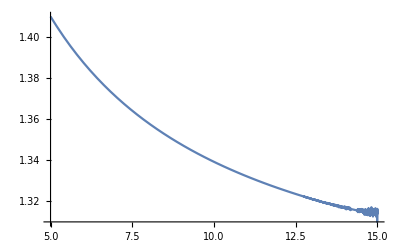

```mathematica
Plot[p[x]Sqrt[x] Exp[x],{x,5,15}]
```

```mathematica
alpha=1/N[Integrate[p[x],{x,0,100}],16]
```

0.1909859317102744

```mathematica
pp[e_]=Integrate[alpha p[x],{x,0,e},Assumptions->e>2]
```

-0.346410161513775 e+0.41052965394701 e^(1/3) (HypergeometricPFQ[{-1/3},{-2/3,2/3},e^2/4]+2 HypergeometricPFQ[{1/6},{-2/3,7/6},e^2/4])-0.0271951368797645 e^(11/3) (1. HypergeometricPFQ[{4/3},{7/3,8/3},e^2/4]-0.727272727272727 HypergeometricPFQ[{11/6},{8/3,17/6},e^2/4])

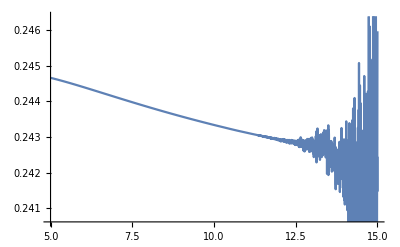

```mathematica
Plot[(1-pp[x])Sqrt[x]Exp[x],{x,5,15}]
```

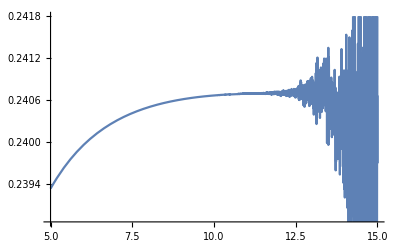

```mathematica
Plot[(1-pp[x]) Sqrt[x] Exp[x]/(1+1/(9x)),{x,5,15}]
```

```mathematica
q[r_]=InverseFunction[pp][r]
```

pp^(-1)[r]

```mathematica
q[0.9999999]
```

13.4043

```mathematica
q'[0.999]
```

903.65

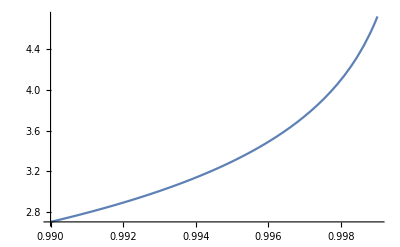

```mathematica
Plot[q[x],{x,0.990,0.999},BaseStyle->{PrintPrecision->6}]
```

```mathematica
NumberForm[Map[q,Range[0.0,0.8,0.02]],8]
```

{-2.2785344+5.2468874 ⅈ,4.2834064×10^-6,0.000034290156,0.00011585842,0.00027505747,0.00053830686,0.00093250004,0.0014851341,0.0022244473,0.0031795668,0.0043806678,0.005859148,0.0076478195,0.0097811211,0.012295356,0.015228961,0.018622804,0.022520536,0.026968982,0.032018597,0.037723996,0.044144571,0.051345214,0.059397173,0.06837907,0.078378116,0.08949158,0.10182857,0.11551222,0.13068237,0.14749895,0.1661462,0.18683808,0.20982519,0.23540392,0.26392847,0.29582721,0.33162503,0.37197493,0.41770346,0.46987814}

```mathematica
NumberForm[Map[q',Range[0.0,0.8,0.02]],8]
```

{1.0358773+0.094620402 ⅈ,0.00064260631,0.00257329,0.0058006813,0.010339284,0.016209659,0.023438687,0.032059915,0.042114002,0.05364926,0.066722326,0.081398955,0.097754987,0.11587748,0.13586608,0.15783464,0.18191312,0.20824993,0.23701467,0.26840143,0.30263281,0.33996474,0.38069245,0.42515766,0.4737576,0.52695612,0.58529771,0.64942516,0.72010211,0.79824218,0.88494687,0.98155565,1.0897128,1.2114583,1.3493529,1.5066541,1.687568,1.8976188,2.1442047,2.4374605,2.7916424}

```mathematica
NumberForm[Map[q,Range[0.80,0.99,0.01]],8]
```

{0.46987814,0.49880667,0.52991104,0.56344857,0.59972426,0.63910329,0.68202787,0.72904042,0.78081609,0.83820971,0.90232524,0.97462245,1.0570871,1.1525166,1.2650292,1.401046,1.5713927,1.7965129,2.1227067,2.6994536}

```mathematica
NumberForm[Map[q',Range[0.80,0.99,0.01]],8]
```

{2.7916424,2.9977025,3.2274448,3.485124,3.7760729,4.1070657,4.4868378,4.9268475,5.4424214,6.0545297,6.7926343,7.6994506,8.8393066,10.313721,12.292676,15.083696,19.305339,26.41041,40.792302,84.662418}

```mathematica
NumberForm[Map[q,Range[0.990,0.999,0.001]],8]
```

{2.6994536,2.7888604,2.8892809,3.0037015,3.1365059,3.2945089,3.4891605,3.7420006,4.1015906,4.7237837}

```mathematica
NumberForm[Map[q',Range[0.990,0.999,0.001]],8]
```

{84.662418,94.500558,106.82986,122.72601,143.98575,173.85088,218.82271,294.11918,445.57461,903.65004}

```mathematica
NumberForm[Map[q,Range[0.9990,0.9999,0.0001]],8]
```

{4.7237837,4.8190811,4.9258192,5.0470809,5.1873871,5.3537566,5.5579673,5.8221404,6.1960561,6.8390833}

```mathematica
NumberForm[Map[q',Range[0.9990,0.9999,0.0001]],8]
```

{903.65004,1005.9104,1133.9035,1298.7019,1518.7818,1827.444,2291.3909,3066.5401,4621.6998,9308.5914}

```mathematica
NumberForm[Map[q,Range[0.99990,0.99999,0.00001]],8]
```

{6.8390833,6.9372066,7.0470098,7.1716317,7.3156733,7.4862732,7.6954033,7.9655326,8.3471796,9.001882}

```mathematica
NumberForm[Map[q',Range[0.99990,0.99999,0.00001]],8]
```

{9308.5914,10352.865,11659.208,13340.208,15583.647,18727.809,23449.897,31331.837,47126.191,94645.923}

```mathematica
NumberForm[Map[q,Range[0.999990,0.999999,0.000001]],8]
```

{9.001882,9.1016308,9.2132088,9.3397903,9.486028,9.6591381,9.8712192,10.144967,10.531391,11.193479}

```mathematica
NumberForm[Map[q',Range[0.999990,0.999999,0.000001]],8]
```

{94645.923,105223.63,118452.33,135469.88,158173.89,189981.63,237732.48,317396.37,476931.1,956469.26}

```mathematica
NumberForm[Map[q,Range[0.9999990,0.9999999,0.0000001]],8]
```

{11.193479,11.294278,11.407001,11.534857,11.682527,11.857289,12.07133,12.347659,12.737582,13.403243}

```mathematica
NumberForm[Map[q',Range[0.9999990,0.9999999,0.0000001]],8]
```

{956469.26,1.0631543×10^6,1.1965692×10^6,1.3681661×10^6,1.5970427×10^6,1.9176469×10^6,2.3987897×10^6,3.2018487×10^6,4.8099726×10^6,9.6282849×10^6}

```mathematica
al=0.000001Sqrt[13.403243]Exp[13.403243]
```

2.42415

```mathematica
f[x_]=al Exp[-x]/Sqrt[x]
```

(2.42415 ⅇ^-x)/(√x)

```mathematica
(2.4241496 ⅇ^-x)/(√x)
```

(2.42415 ⅇ^-x)/(√x)

```mathematica
f[31.4]
```

9.9827×10^-15